# The Lorentz factor has a Maclaurin series

```mathematica
Clear["Global`*"]
```

## Ex

### Speed of light

```mathematica
c:=1
```

```mathematica
(*c:=299792458*)
```

### Relative velocity

```mathematica
v=0.8c
```

0.8

### Ratio of v to the speed of light c

```mathematica
β=v/c
```

0.8

### Lorentz factor

```mathematica
γ=1/(√(1-β^2))
```

1.66667

## Generalisation

```mathematica
Clear["Global`*"]
```

```mathematica
c:=1
```

```mathematica
(*c:=299792458*)
```

```mathematica
β[v_]:=v/c
```

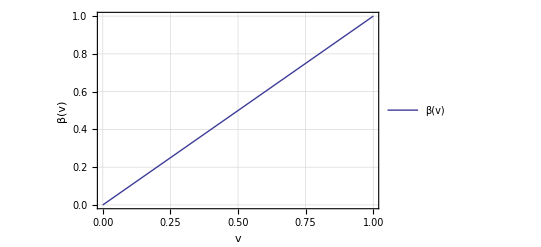

```mathematica
Plot[β[v],{v,0,c},AxesLabel->{"v","β(v)"},PlotLegends->"Expressions",Frame-> True,GridLines->Automatic]
```

```mathematica
γ[β_]:=1/(√(1-β^2))
```

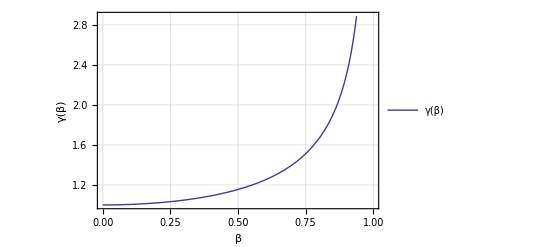

```mathematica
Plot[γ[β],{β,0,1},AxesLabel->{"β","γ(β)"},PlotLegends->"Expressions",Frame-> True,GridLines->Automatic]
```

### The Lorentz factor has a Maclaurin series of

```mathematica
Maclaurin=Series[γ[β],{β,0,5}]
```

1+β^2/2+(3 β^4)/8+O[β]^6

```mathematica
p1=Plot[γ[β],{β,0,1},PlotLegends->"Expressions",Frame-> True,GridLines->Automatic];
```

```mathematica
p2=Plot[Evaluate[Normal[Maclaurin]],{β,0,1},PlotStyle->Directive[Red],PlotLegends->"Expressions",Frame-> True,GridLines->Automatic];
```

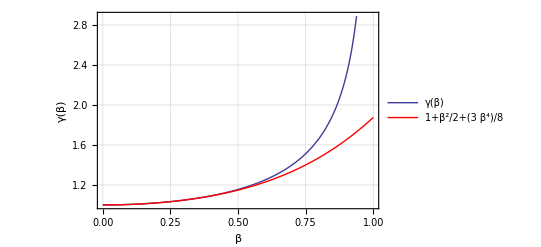

```mathematica
Show[p1,p2,AxesLabel->{"β","γ(β)"}]
```